```mathematica
1/(1+exp(-z))
```

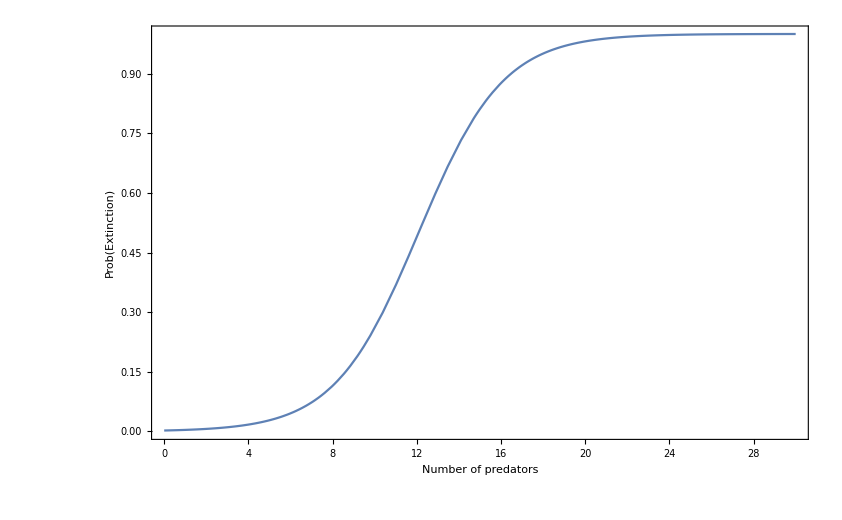

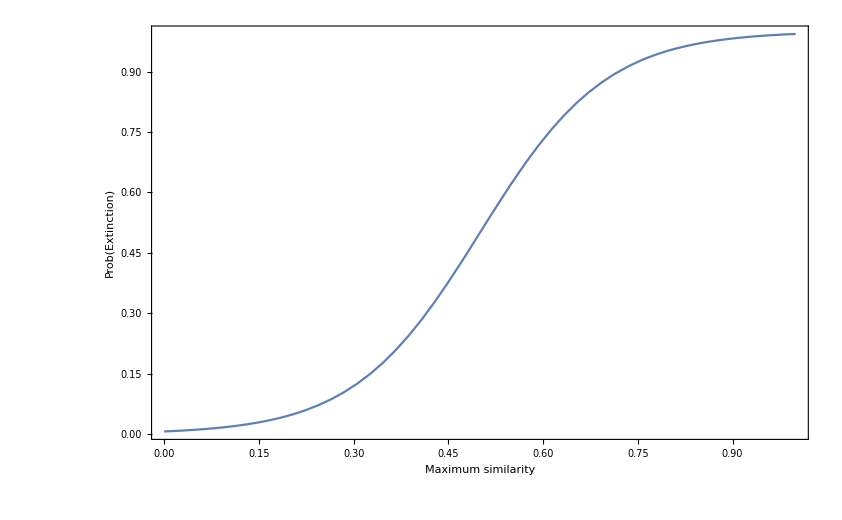

```mathematica
PredCurve = 1/(1+Exp[-0.5(x-2(L/S))]);
CompCurve = 1/(1+Exp[-10*(y-0.5)]);
Plot[PredCurve/.{L->2000,S->331},{x,0,30},PlotRange->{0,1},Frame->True,FrameLabel->{"Number of predators","Prob(Extinction)"}]
Plot[CompCurve,{y,0,1},PlotRange->All,Frame->True,FrameLabel->{"Maximum similarity","Prob(Extinction)"}]
```

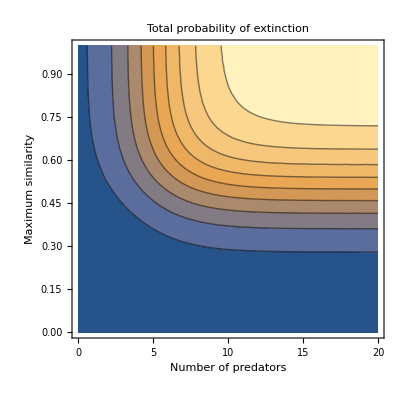

```mathematica
ContourPlot[PredCurve*CompCurve/.{L->1500,S->300},{x,0,20},{y,0,1},PlotRange->All,FrameLabel->{"Number of predators","Maximum similarity"},PlotLabel->"Total probability of extinction"]
```